# Towards Universal Robotics

Douw Marx

University of Pretoria

Background: Universal robotics

Overview: 

Results:

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

### What is Universal Robotics?

#### What is universal robotics?

Simulate any other robot compare to universal Turing machine

Image/ meme about robots. ( Anything you can do I can do uhm yes thats it.)

#### Parallel between universal computing and universal robotics.

Idea that we don’t have fully universal computing and would probably also not have fully universal robotics

#### How would we know if we have achieved general robotics?

Position, Force, Computation

### Overview

Each of the criteria required for general robotics in discussed. This include performing arbitrary motion, resisting or applying arbitrary force and universality

### Arbitrary Motion

#### Inverse Kinematics

Traditional methods for determining what the input to a robot should be to move it to a certain point in space include inverse kinematics.

```mathematica
ListAnimate[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Essentially, this evolves solving a optimisation problem. The optimal actuator lengths are found given the desired end effector position and other constraints such as minimum and maximum possible actuator lengths and possible collision with itself and its surroundings. Traditional approach becomes significantly harder as the number of members increase since the number of unknowns in the optimisation problem increases as well.

#### Discrete Robotics and State Transition Diagrams

Random states for structure that consists only of triangles with no redundant modules and having one of 2 possible states for each module (60% ->100%)

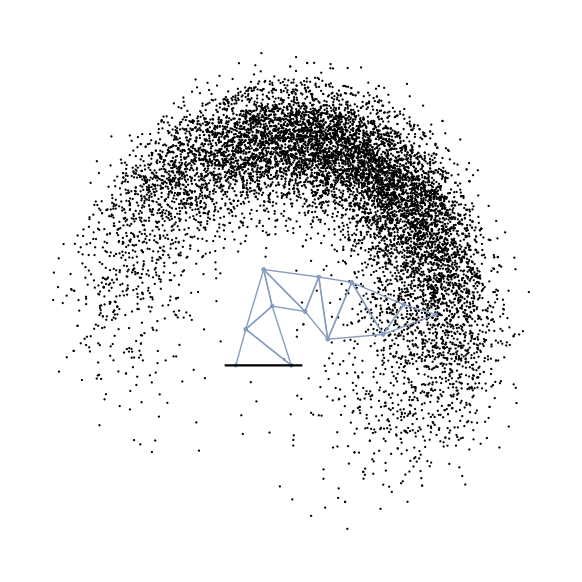

Transition between states in a certain order. Approximating continuous motion to an arbitrary precision

We can create a state transition diagram for all the possible states the system could be in and how it would transition between states. This state transition diagram has to account for things like collisions and the appropriate force as discusses later

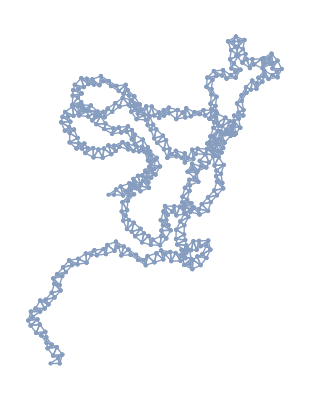

If the robot is allowed to change the length of single actuator every timestepState transition diagram below. Does not account for collisions but they are not so likely here.
-Graphics-

From this graph, you can for instance get the shortest path in transitioning between states or choose a path that would lead to the smoothest transition or no collisions.

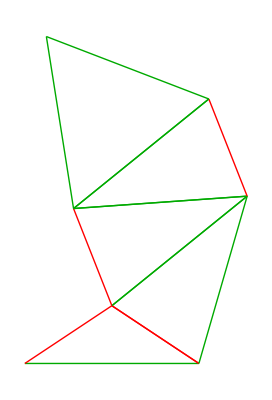
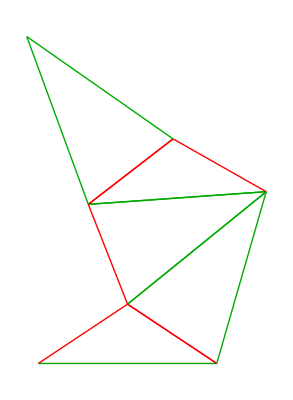
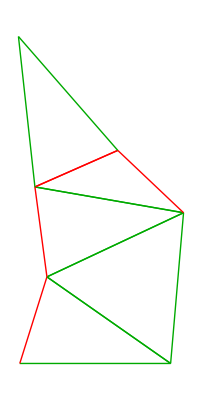
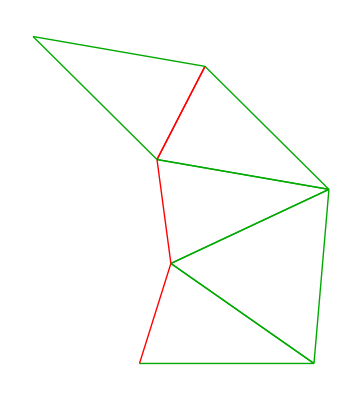
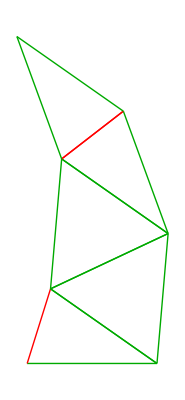
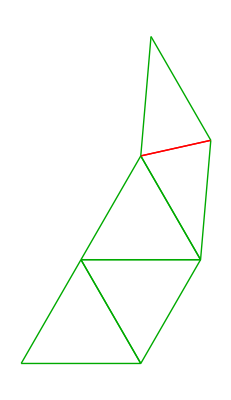
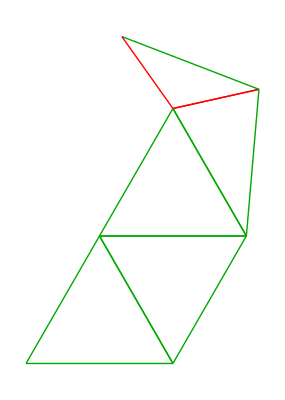
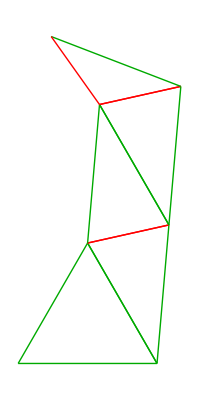

#### Rule-based Position control

Rule plot with rule used?

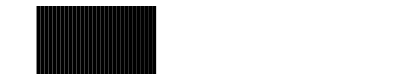
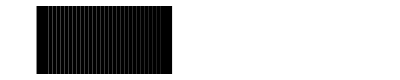
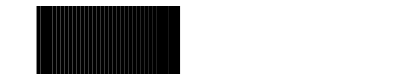
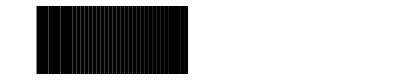
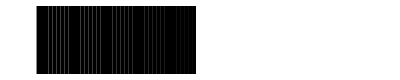
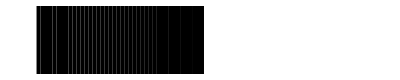
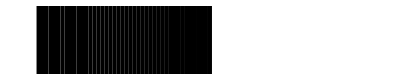
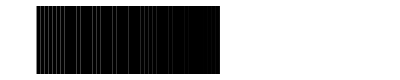
```mathematica
ListAnimate[{{{"Apply rule 0 times"}, {-Graphics-}},{{"Apply rule 1 times"}, {-Graphics-}},{{"Apply rule 2 times"}, {-Graphics-}},{{"Apply rule 3 times"}, {-Graphics-}},{{"Apply rule 29 times"}, {-Graphics-}},{{"Apply rule 4 times"}, {-Graphics-}},{{"Apply rule 5 times"}, {-Graphics-}},{{"Apply rule 576 times"}, {-Graphics-}},{{"Apply rule 10 times"}, {-Graphics-}},{{"Apply rule 13 times"}, {-Graphics-}},{{"Apply rule 44 times"}, {-Graphics-}},{{"Apply rule 8 times"}, {-Graphics-}},{{"Apply rule 9 times"}, {-Graphics-}},{{"Apply rule 15 times"}, {-Graphics-}},{{"Apply rule 11 times"}, {-Graphics-}},{{"Apply rule 25 times"}, {-Graphics-}},{{"Apply rule 18 times"}, {-Graphics-}},{{"Apply rule 33 times"}, {-Graphics-}},{{"Apply rule 17 times"}, {-Graphics-}},{{"Apply rule 27 times"}, {-Graphics-}},{{"Apply rule 47 times"}, {-Graphics-}},{{"Apply rule 16 times"}, {-Graphics-}},{{"Apply rule 65 times"}, {-Graphics-}},{{"Apply rule 215 times"}, {-Graphics-}},{{"Apply rule 63 times"}, {-Graphics-}},{{"Apply rule 1885 times"}, {-Graphics-}}},3]
```

This is still rule based control and does not include a computational aspect of updating the states

### Arbitrary Force

Idea that you could add rods to increase ability to withstand force mention the need for a hat and that the structure should be rigid

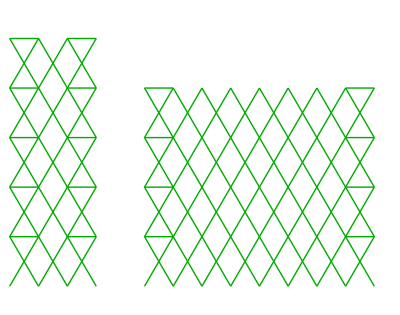

Idea of building blocks of building blocks - rods,wedges turns.

Mention apparent relationship between space and for

### Universal Computation

As a preliminary investigation into the universal computation for universal robotics a one-dimensional problem is considiered:

Start with a single rod and grow it and stuf

ok?

Show that you can have complex behaviour and that you can effectively do the same as rule 110. There are 2^16 = 65536 possible rules that show similar behaviour to the elementary cellular automata. A rule like 51051 shows behaviour that could indicate that it can be capable of universal computation.

```mathematica
rule51051 = ;
nevol = 1000;init={2,0,1,0,2};
evol51051 = NestList[Last@CellularAutomaton[rule51051,Join[{2,0},#[[2;;-1]]],1]&,init,nevol];
ArrayPlot[evol51051]
```

-Graphics-

Realizing that we can simulate any arbitrary cellular automata this way seeing that we are effetively generating an all white background

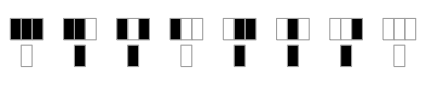

RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[1]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[1]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[1]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]
RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]

```mathematica
rod110 = {{2,0,0}->1,{2,0,1}->1,{2,1,0}->0,{2,1,1}->0,{0,0,0}->0,{0,0,1}->1,{0,1,0}->1,{0,1,1}->1,{1,0,0}->0,{1,0,1}->1,{1,1,0}->1,{1,1,1}->0,{0,0,2}->0,{0,1,2}->0,{1,0,2}->0,{1,1,2}->0,{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2};
RulePlot[CellularAutomaton[110]]
Row[Framed@Column[{Row[#1],#2}/.{0->White,1->Black,2->Darker@Red},Center]&@@@rod110]
```

```mathematica
nevol = 1000;init={2,0,1,0,2};
evol = PadLeft[NestList[Last@CellularAutomaton[rod110,Join[{2,0},#[[2;;-1]]],1]&,init,nevol]];
ArrayPlot[evol]
```

1000

-Graphics-

In fact they are identical

```mathematica
evolrem2 = evol/. 2->0 ;  (*Repalce the edges (2) with 0's*)
 evolrem2[[2;;-2,3;;-3]]==CellularAutomaton[110,{{1},0},nevol][[3;;-1,All]] (*Make sure the shapes alling*)
```

True

### Simplifications and Alternatives

Means of actuation, 1D,2D vs 3D

<one-line text, explaining the code only> Plot several functions with a legend:

For the full project notebook an supporting packages, please visit www.notebookarchive  or https://github.com/DouwMarx/wolfram_summer_school

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

## Keywords

Robotics

Universality

Cellular Automata

Modular

## Acknowledgment

Mentor: Philip Maymin

<text>

## References

<Ref1>

<Ref2>

...